# spectrum

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Level statistics\\QKT_nomemory.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Method

```mathematica
(*Parameters*)
Jmin=1;    (*Start J*)
Jmax=100;    (*End J*)
step=1;      (*Step size*)
α=0.84;
k=15.0;
(*Output Directories*)
baseDir=NotebookDirectory[]<>"Data_eigenvalues";
dirEven=FileNameJoin[{baseDir,"Even"}];
dirOdd=FileNameJoin[{baseDir,"Odd"}];
(*Create directories if they don't exist*)
If[!DirectoryQ[baseDir],CreateDirectory[baseDir]];
If[!DirectoryQ[dirEven],CreateDirectory[dirEven]];
If[!DirectoryQ[dirOdd],CreateDirectory[dirOdd]];
```

```mathematica
(* ==========================================*)
(*2. DEFINITIONS (Distribute to Kernels)*)
(* ==========================================*)
(*Standard Quantum Kicked Top Floquet Operator*)
(*U=Exp[-i (k/2J) Jz^2].Exp[-i alpha Jy]*)
(*Floq[jVal_,alpha_,kVal_]:=Module[{d,mRange,Jz,Jy,Kicked,Rot},d=2 jVal+1;
mRange=Range[jVal,-jVal,-1];
(*Diagonal Kick Operator (Jz is diagonal in this basis)*)(*Note:We use N[] to ensure machine precision for speed*)Kicked=DiagonalMatrix[Exp[-I (kVal/(2 jVal))*mRange^2]];
(*Rotation Operator (Jy construction)*)(*For large J,RotationMatrix is efficient*)(*Alternatively,construct Jy explicitly if needed for specific basis conventions*)Rot=WignerD[{jVal,alpha,0,0}];(*Efficient built-in rotation matrix for Jy*)(*Total Floquet Operator*)Return[Kicked.Rot];];*)
```

```mathematica
(*Helper to process a single J*)
Clear[ProcessJ];
ProcessJ[jVal_,alpha_,kVal_,dEven_,dOdd_]:=Module[{mat,matEven,matOdd,evalsEven,evalsOdd,fileEven,fileOdd},
(*1. Construct Full Matrix*)
mat=Floq[jVal,alpha,kVal];
(*2. Split by Parity (Standard Basis: |j,m>parity alternates)*)(*Even Parity:Indices 1,3,5...*)
matEven=mat[[1;; ;;2,1;; ;;2]];
matOdd=mat[[2;; ;;2,2;; ;;2]];
evalsEven=Eigenvalues[matEven,Method->"Direct"];
evalsOdd=Eigenvalues[matOdd,Method->"Direct"];
fileEven=FileNameJoin[{dEven,"evals_J_"<>ToString[jVal]<>".mx"}];
fileOdd=FileNameJoin[{dOdd,"evals_J_"<>ToString[jVal]<>".mx"}];
Export[fileEven,evalsEven];
Export[fileOdd,evalsOdd];
jVal];
DistributeDefinitions[Floq,ProcessJ];
```

```mathematica
Print["Starting calculation for J = ",Jmin," to ",Jmax];
(*ParallelDo splits the list of J values across cores*)
ParallelDo[ProcessJ[jCurrent,α,k,dirEven,dirOdd],{jCurrent,Jmin,Jmax,step},Method->"FinestGrained" (*Better load balancing if times vary*)];
Print["Done! Files saved in: ",baseDir];
```

Starting calculation for J = 1 to 100

Done! Files saved in: C:\Users\Miguel\Github\Chaotic_eigenfunctions\Level statistics\Data_eigenvalues

# Lenght spectra

## Tests just trace

```mathematica
(*Floquet parameters*)
α=0.84;
k=15.;
```

```mathematica
(*FASTEST METHOD for Period 1*)
Clear[AnalyzeSpectrumFast];
AnalyzeSpectrumFast[maxJ_,k_]:=Module[{jValues=Range[1,maxJ,1],traceData,len,window,fft,freqs,amps},
(*Parallelize the J loop*)
traceData=ParallelTable[Tr[Floq[j,α,k]],{j,jValues},Method->"CoarsestGrained"];
len=Length[traceData];
window=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
fft=Fourier[(traceData-Mean[traceData])*window];
freqs=Table[(i-1)*(2 Pi/len),{i,1,Floor[len/2]}];
amps=Abs[fft[[1;;Floor[len/2]]]];
Transpose[{freqs,amps}]];
```

```mathematica
(*---EXECUTION---*)
(*We compute ONCE for the largest range (500)*)
(*This replaces the repetitive loop in your previous code*)
maxJ=200;
```

```mathematica
{timeDiag,data}=AbsoluteTiming[AnalyzeSpectrumFast[maxJ,k]];
Print["Diagonalization Complete. Time: ",timeDiag," seconds."];
```

Diagonalization Complete. Time: 18.6927 seconds.

```mathematica
(*---PLOTTING---*)
(*Define Styles*)
myStyles=Table[Directive[Opacity[0.8],Thickness[0.002],ColorData[97][i]],{i,1,Length[jRanges]}];
myLegendLabels=("J_max = "<>ToString[#])&/@jRanges;
```

```mathematica
ListPlot[data,PlotStyle->myStyles,PlotLegends->Placed[LineLegend[myLegendLabels,LegendLabel->"Semiclassical Depth"],{Right,Top}],Frame->True,FrameLabel->{Style["Classical Action S (0 to 2π)",18,Black],Style["|Trace Amplitude|",18,Black]},PlotLabel->Style["Trace Formula \n(Period "<>ToString[scanPeriod]<>", K="<>ToString[k]<>")",16,FontFamily->"Helvetica"],GridLines->{Automatic,Automatic},Filling->Bottom,ImageSize->Large,PlotRange->All]
```

```mathematica
(* ==========================================*)(*1. PARAMETERS& DEFINITIONS*)(* ==========================================*)(*Floquet parameters*)
α=0.84;
k=15.;
scanPeriod=1; (*Defined for labeling purposes*)

(*FASTEST METHOD for Period 1-FULL SPECTRUM FIX*)
Clear[AnalyzeSpectrumFast];
AnalyzeSpectrumFast[maxJ_,k_]:=Module[{jValues=Range[1,maxJ,1],traceData,len,window,fft,freqs,amps},
traceData=ParallelTable[Tr[Floq[j,α,k]],{j,jValues},Method->"CoarsestGrained"];
(*2. Process FFT*)len=Length[traceData];
window=Table[HannWindow[(i-1)/(len-1)-1/2],{i,1,len}];
(*Remove DC component (Identity trace) and Window*)fft=Fourier[(traceData-Mean[traceData])*window];
(*3. SCALING:FULL RANGE[0,2Pi]*)(*CHANGE:We now iterate'i' up to'len' (Full DFT)*)freqs=Table[(i-1)*(2. Pi/len),{i,1,len}];
(*CHANGE:We take the Absolute value of the FULL fft list*)amps=Abs[fft];
Transpose[{freqs,amps}]];
```

```mathematica
(* ==========================================*)
(*2. EXECUTION*)
(* ==========================================*)
maxJ=1000;
Print["Computing Trace for J=1 to ",maxJ,"..."];
{timeDiag,data}=AbsoluteTiming[AnalyzeSpectrumFast[maxJ,k]];
Print["Computation Complete. Time: ",timeDiag," seconds."];
```

Computing Trace for J=1 to 1000...

Computation Complete. Time: 6216.62 seconds.

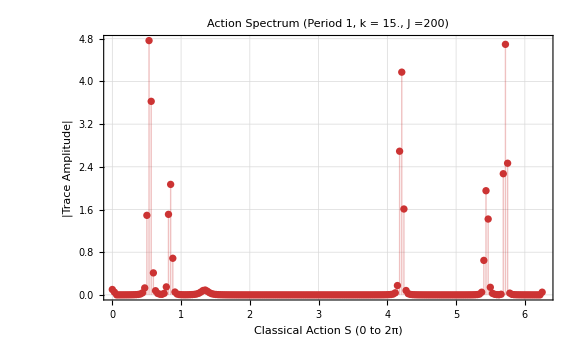

```mathematica
(* ==========================================*)
(*3. PLOTTING*)
(* ==========================================*)
ListPlot[data,(*Styles*)PlotStyle->Directive[RGBColor[0.8,0.2,0.2],Thickness[0.003]],Filling->Bottom,(*Axes& Labels*)Frame->True,FrameLabel->{Style["Classical Action S (0 to 2π)",18,Black],Style["|Trace Amplitude|",18,Black]},PlotLabel->Style["Action Spectrum\n(Period "<>ToString[scanPeriod]<>", k = "<>ToString[k]<>", J ="<>ToString[maxJ]<>")",16,FontFamily->"Helvetica"],(*Full Range View*)PlotRange->{{0,2 Pi},All},GridLines->{Automatic,Automatic},ImageSize->Large]
```